```mathematica
(* relation of EER as a function of the  number of features
PCA.nb*)
ee=Import["Cache_edat.mx"];
```

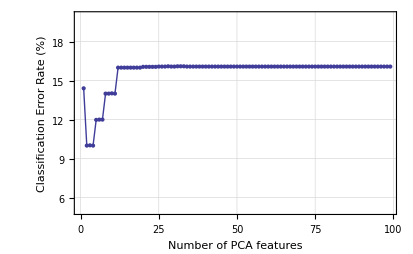

```mathematica
ListPlot[100*ee,Joined->True,PlotRange->{5,20},Mesh->Full,Frame->True,FrameLabel->{"Number of PCA features","Classification Error Rate (%)"},GridLines->Automatic]
```

```mathematica
(* after MDA ordering*)
ee=Import["Cache_ePcamda.mx"];
```

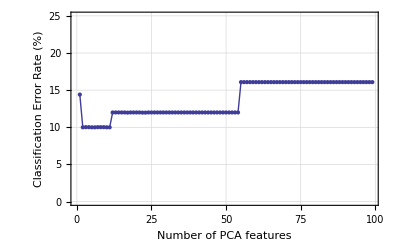

```mathematica
ListPlot[100*ee,Joined->True,PlotRange->{0,25},Mesh->Full,Frame->True,FrameLabel->{"Number of PCA features","Classification Error Rate (%)"},GridLines->Automatic]
```

```mathematica
(*PCA.nb J1 relation*)
```

```mathematica
pc=PrincipalComponents [sample];
Dimensions[pc]
tpc=pc[[All,;;99]];
```

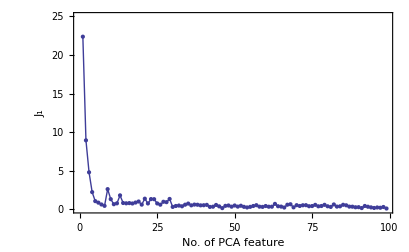

```mathematica
ListPlot[sj1,Joined->True,Mesh->Full,PlotRange->{0,25},Frame->True,FrameLabel->{"No. of PCA feature","J_1"}]
```